```mathematica
s0 = ({{1, 0}, {0, 1}});
sx = ({{0, 1}, {1, 0}});
sy = ({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
```

```mathematica
I0[L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
X[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sx;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Y[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sy;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Z[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sz;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
X1 = X[1,3];
Y1 = Y[1,3];
Z1 = Z[1,3];
X2 = X[2,3];
Y2 = Y[2,3];
Z2 = Z[2,3];
X3 = X[3,3];
Y3 = Y[3,3];
Z3 = Z[3,3];
```

## Start with the Hamiltonian

This is a three qubit version of the Hamiltonian in Rigetti, Devoret 2010.  We will do the same initial tricks to rotate this into a frame without single qubit terms.  Then we will choose parameters so that the two qubit terms are relatively simple.  Finally the plan will be to do some two qubit rotation to find a frame where there are only three qubit terms.

```mathematica
H = 1/2 ω1 Z1+1/2 ω2 Z2+1/2 ω3 Z3+Ω1 Cos[ωr1 t +ϕ1] X1+Ω2 Cos[ωr2 t +ϕ2]X2+Ω3 Cos[ωr3 t +ϕ3]X3+1/2 ω12 X1.X2+1/2 ω23 X2.X3+1/2 ω31 X3.X1;
```

## First we apply these two unitarity operators to remove time dependance.

Since Pauli operators on different sites commute, adding the third qubit does not change the rotations.  These will do exactly what they do in the paper.  Note that because Ua is time dependent, we cannot just apply it in the normal way.  According to the paper the frame changes as :
						H'=U_a^-1 HU_a-ⅈ U_a^-1 dU_a/dt

```mathematica
Ua =( Cos[(t ωr1)/2]I0[3]-ⅈ Sin[(t ωr1)/2]Z1).( Cos[(t ωr2)/2]I0[3]-ⅈ Sin[(t ωr2)/2]Z2).( Cos[(t ωr3)/2]I0[3]-ⅈ Sin[(t ωr3)/2]Z3);
Uad=( Cos[(t ωr1)/2]I0[3]+ⅈ Sin[(t ωr1)/2]Z1).( Cos[(t ωr2)/2]I0[3]+ⅈ Sin[(t ωr2)/2]Z2).( Cos[(t ωr3)/2]I0[3]+ⅈ Sin[(t ωr3)/2]Z3);
UadUa = -ⅈ/2 ωr1 Z1-ⅈ/2 ωr2 Z2-ⅈ/2 ωr3 Z3;
```

```mathematica
Ub = ( Cos[ϕ1/2]I0[3]-ⅈ Sin[ϕ1/2]Z1).( Cos[ϕ2/2]I0[3]-ⅈ Sin[ϕ2/2]Z2).( Cos[ϕ3/2]I0[3]-ⅈ Sin[ϕ3/2]Z3);
Ubd = ( Cos[ϕ1/2]I0[3]+ⅈ Sin[ϕ1/2]Z1).( Cos[ϕ2/2]I0[3]+ⅈ Sin[ϕ2/2]Z2).( Cos[ϕ3/2]I0[3]+ⅈ Sin[ϕ3/2]Z3);
```

### Let’s check each term individually. First look at 1/2 ω_1 Z_1

```mathematica
Simplify[1/2 ω1 Z1-Ubd.Uad.(1/2 ω1 Z1).Ua.Ub]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

This term does not change since it commutes with both operators.  By analogy, the Z2 and Z3 terms will also be unchanged.

### Ω_1 Cos[ωr1 t +ϕ1]X_1

```mathematica
Simplify[Ω1 Cos[ωr1 t +ϕ1]( Cos[t ωr1+ϕ1]I0[3]+ⅈ Sin[t ωr1+ϕ1]Z1).X1 -Ubd.Uad.(Ω1 Cos[ωr1 t +ϕ1]X1).Ua.Ub]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

At this point, the paper invokes the “rotating wave approximation”  where they claim that the time dependance approximately vanishes since it goes as 2*ω^rf instead of ω^rf.   Using:
									Cos[a]^2 = 1/2(1+Cos[2 a])
									Cos[a]Sin[a] = Sin[2a]
We see that the time dependance can be eliminated. 
								
Let us take a look at the plot before moving on.

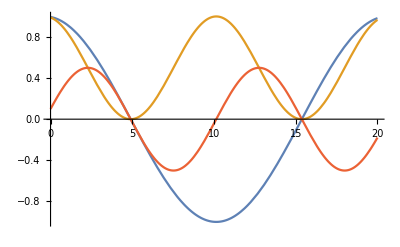

```mathematica
Plot[{Cos[0.3*t+0.1],Cos[0.3*t+0.1]Cos[0.3*t+0.1],,Cos[0.3*t+0.1]Sin[0.3*t+0.1]},{t,0,20}]
```

We see that the Sin term averages to zero while the Cos term averages to 1/2.  

The Z2 and Z3 terms can be found by analogy.

### 1/2 ω_12 X_1 X_2

```mathematica
Simplify[1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2)-Ubd.Uad.(1/2 ω12 X1.X2).Ua.Ub]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The X2 X3 and X3 X1 terms can be found by analogy.

### Now put it all together

Let’s test that we get the exact solution without the rotating wave approximation, then we will take the approximation.

```mathematica
Simplify[1/2 ω1 Z1+1/2 ω2 Z2+1/2 ω3 Z3+Ω1 Cos[ωr1 t +ϕ1]( Cos[t ωr1+ϕ1]I0[3]+ⅈ Sin[t ωr1+ϕ1]Z1).X1 +Ω2 Cos[ωr2 t +ϕ2]( Cos[t ωr2+ϕ2]I0[3]+ⅈ Sin[t ωr2+ϕ2]Z2).X2 +Ω3 Cos[ωr3 t +ϕ3]( Cos[t ωr3+ϕ3]I0[3]+ⅈ Sin[t ωr3+ϕ3]Z3).X3 +1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2)+1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3)+1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1)-Ubd.Uad.H.Ua.Ub]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Now we take the approximation and add in the  -ⅈ U_a^-1 dU_a/dtfrom the time dependence of Ua

```mathematica
δ1=(ω1-ωr1);
δ2=(ω2-ωr2);
δ3=(ω3-ωr3);
HRF =1/2 δ1 Z1+1/2 Z2+1/2 δ3 Z3+1/2 Ω1 X1 +1/2 Ω2 X2 +1/2 Ω3 X3 +1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2)+1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3)+1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
```

## Now we rotate out the single qubit terms

If we were not already given the parameters then we could try a general rotation and then solve for the parameters but the parameters from the paper will work.

```mathematica
η1=√(δ1^2+Ω1^2);
η2 = √(δ2^2+Ω2^2);
η3 = √(δ2^2+Ω3^2);
ζ1=ArcTan[δ1/Ω1];
ζ2=ArcTan[δ2/Ω2];
ζ3=ArcTan[δ2/Ω3];
Clear[η1,η2,η3,ζ1,ζ2,ζ3,δ1,δ2,δ3]
Uc =( Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).( Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).( Cos[ζ3/2]I0[3]+ⅈ Sin[ζ3/2]Y3);
Ucd =( Cos[ζ1/2]I0[3]-ⅈ Sin[ζ1/2]Y1).( Cos[ζ2/2]I0[3]-ⅈ Sin[ζ2/2]Y2).( Cos[ζ3/2]I0[3]-ⅈ Sin[ζ3/2]Y3); 

Ud =( Cos[(η1 t)/2]I0[3]-ⅈ Sin[(η1 t)/2]X1).( Cos[(η2 t)/2]I0[3]-ⅈ Sin[(η2 t)/2]X2).( Cos[(η3 t)/2]I0[3]-ⅈ Sin[(η3 t)/2]X3);
Udd =( Cos[(η1 t)/2]I0[3]+ⅈ Sin[(η1 t)/2]X1).( Cos[(η2 t)/2]I0[3]+ⅈ Sin[(η2 t)/2]X2).( Cos[(η3 t)/2]I0[3]+ⅈ Sin[(η3 t)/2]X3); 

UddUd=-ⅈ 1/2 η1 X1-ⅈ 1/2 η2 X2-ⅈ 1/2 η3 X3;
```

### 1/2 δ_1 Z_1

```mathematica
Simplify[1/2 δ1 ( Cos[ζ1]( Cos[η1 t]Z1+ Sin[η1 t]Y1)+Sin[ζ1]X1)-Udd.Ucd.(1/2 δ1 Z1).Uc.Ud]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### 1/2 Ω_1 X_1

```mathematica
Simplify[1/2 Ω1 ( Cos[ζ1]X1 -Sin[ζ1]( Cos[η1 t]Z1+Sin[η1 t]Y1))-Udd.Ucd.(1/2 Ω1 X1 ).Uc.Ud]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### 1/2 δ_1 Z_1+ 1/2 Ω_1 X_1

```mathematica
Simplify[1/2 δ1 ( Cos[ζ1]( Cos[η1 t]Z1+ Sin[η1 t]Y1)+Sin[ζ1]X1)+1/2 Ω1 ( Cos[ζ1]X1 -Sin[ζ1]( Cos[η1 t]Z1+Sin[η1 t]Y1))-Udd.Ucd.(1/2 δ1 Z1+1/2 Ω1 X1 ).Uc.Ud]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Let’s check that this cancels.  Keep in mind that we also have a term 1/2 η1 X1 from the time dependance of Ud.

```mathematica
η1=√(δ1^2+Ω1^2);
ζ1=ArcTan[δ1/Ω1];
```

```mathematica
test = 1/2 δ1 ( Cos[ζ1]( Cos[η1 t]Z1+ Sin[η1 t]Y1)+Sin[ζ1]X1)+1/2 Ω1 ( Cos[ζ1]X1 -Sin[ζ1]( Cos[η1 t]Z1+Sin[η1 t]Y1));
```

```mathematica
Simplify[(1/2 δ1  Cos[ζ1] Cos[η1 t]-1/2 Ω1 Sin[ζ1] Cos[η1 t])Z1+(1/2 δ1  Cos[ζ1]Sin[η1 t]-1/2 Ω1 Sin[ζ1]Sin[η1 t])Y1+(1/2 δ1 Sin[ζ1]+  1/2 Ω1 Cos[ζ1])X1 -test]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The Z1 term is:

```mathematica
tstZ = (1/2 δ1  Cos[ζ1] Cos[η1 t]-1/2 Ω1 Sin[ζ1] Cos[η1 t]);
```

```mathematica
1/2(δ1  Cos[ArcTan[δ1/Ω1]]-Ω1 Sin[ArcTan[δ1/Ω1]] ) Cos[η1 t]-tstZ
```

0

```mathematica
1/2(δ1  1/(√(1+(δ1/Ω1)^2))-Ω1 (δ1/Ω1)/(√(1+(δ1/Ω1)^2)) ) Cos[η1 t]-tstZ
```

0

```mathematica
0-tstZ
```

0

The Y1 term is:

```mathematica
tstY=(1/2 δ1  Cos[ζ1]Sin[η1 t]-1/2 Ω1 Sin[ζ1]Sin[η1 t]);
```

```mathematica
1/2(δ1  Cos[ArcTan[δ1/Ω1]]-Ω1 Sin[ArcTan[δ1/Ω1]])Sin[η1 t]-tstY
```

0

```mathematica
1/2(δ1  1/(√(1+(δ1/Ω1)^2))-Ω1 (δ1/Ω1)/(√(1+(δ1/Ω1)^2)))Sin[η1 t]-tstY
```

0

```mathematica
0-tstY
```

0

The X1 term is:

```mathematica
tstX=(1/2 δ1 Sin[ζ1]+  1/2 Ω1 Cos[ζ1])X1;
```

```mathematica
Simplify[ 1/2(δ1 Sin[ArcTan[δ1/Ω1]]+ Ω1 Cos[ArcTan[δ1/Ω1]])X1-tstX]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[ 1/2(δ1^2/(√((Ω1)^2+(δ1)^2))+  Ω1^2/(√((Ω1)^2+(δ1)^2)))X1-tstX,Ω1>0]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[ 1/2 √((Ω1)^2+(δ1)^2)X1-tstX,Ω1>0]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[ 1/2 η1 X1-tstX,Ω1>0]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

This exactly cancels with the term from the time dependance of Ud.

### The ω12 term

```mathematica
Clear[η1,η2,η3,ζ1,ζ2,ζ3,δ1,δ2,δ3]
```

```mathematica
Simplify[1/2 ω12 ( Cos[(η1 t)/2]I0[3]+ⅈ Sin[(η1 t)/2]X1).( Cos[ζ1/2]I0[3]-ⅈ Sin[ζ1/2]Y1).( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).( Cos[(η1 t)/2]I0[3]-ⅈ Sin[(η1 t)/2]X1).( Cos[(η2 t)/2]I0[3]+ⅈ Sin[(η2 t)/2]X2).( Cos[ζ2/2]I0[3]-ⅈ Sin[ζ2/2]Y2).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).( Cos[(η2 t)/2]I0[3]-ⅈ Sin[(η2 t)/2]X2)-1/2 ω12 Udd.Ucd.( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).Uc.Ud]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

We can do the rotation for qubit 1 and then the rotation for qubit 2 follows from analogy.

```mathematica
tstQ1 = ( Cos[(η1 t)/2]I0[3]+ⅈ Sin[(η1 t)/2]X1).( Cos[ζ1/2]I0[3]-ⅈ Sin[ζ1/2]Y1).( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).( Cos[(η1 t)/2]I0[3]-ⅈ Sin[(η1 t)/2]X1);
```

```mathematica
Simplify[( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1))-tstQ1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The second qubit term is exactly the same with 1 → 2

### Now put it all together

Mathematica is not going to want to simplify the entire thing so let’s pick some test values for the parameters.

```mathematica
ω1 = 0.35;
ω2=0.67;
ω3=0.14;
ωr1=0.98;
ωr2=0.77;
ωr3=0.93;
Ω1 = 1.26;
Ω2=0.42;
Ω3=0.63;
t=3.9;
ϕ1=0.57;
ϕ2=0.48;
ϕ3=0.88;
ω12=1.31;
ω23=0.75;
ω31=1.17;
δ1=(ω1-ωr1);
δ2=(ω2-ωr2);
δ3=(ω3-ωr3);
η1 = √(δ1^2+Ω1^2);
η2 = √(δ2^2+Ω2^2);
η3 = √(δ3^2+Ω3^2);
ζ1=ArcTan[δ1/Ω1];
ζ2=ArcTan[δ2/Ω2];
ζ3=ArcTan[δ3/Ω3];

Uc =( Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).( Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).( Cos[ζ3/2]I0[3]+ⅈ Sin[ζ3/2]Y3);
Ucd =( Cos[ζ1/2]I0[3]-ⅈ Sin[ζ1/2]Y1).( Cos[ζ2/2]I0[3]-ⅈ Sin[ζ2/2]Y2).( Cos[ζ3/2]I0[3]-ⅈ Sin[ζ3/2]Y3); 

Ud =( Cos[(η1 t)/2]I0[3]-ⅈ Sin[(η1 t)/2]X1).( Cos[(η2 t)/2]I0[3]-ⅈ Sin[(η2 t)/2]X2).( Cos[(η3 t)/2]I0[3]-ⅈ Sin[(η3 t)/2]X3);
Udd =( Cos[(η1 t)/2]I0[3]+ⅈ Sin[(η1 t)/2]X1).( Cos[(η2 t)/2]I0[3]+ⅈ Sin[(η2 t)/2]X2).( Cos[(η3 t)/2]I0[3]+ⅈ Sin[(η3 t)/2]X3); 

UddUd=-ⅈ 1/2 η1 X1-ⅈ 1/2 η2 X2-ⅈ 1/2 η3 X3;
HRF =1/2 δ1 Z1+1/2 δ2 Z2+1/2 δ3 Z3+1/2 Ω1 X1 +1/2 Ω2 X2 +1/2 Ω3 X3 +1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2)+1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3)+1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
```

```mathematica
Max[Abs[1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2))+1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3))+1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1))-(Udd.Ucd.HRF.Uc.Ud-ⅈ UddUd)]]
```

5.38916×10^-16

So we can write the Hamiltonian without any single qubit terms

```mathematica
HQF=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2))+1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3))+1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1));
```

## Cross resonance parameters.

The ω12 and ω23 terms can be greatly simplified by taking the cross resonance parameters.  It is unclear what will happen to the ω31 term but we can check.  The parameters are:

ωr1 → ω2
ωr2 → ω2
ωr3 → ω2
Ω2 → 0
ϕ2 → 0

where we take δ2 → 0 faster than Ω2 → 0

```mathematica
ω1 = 0.35;
ω2=0.67;
ω3=0.14;
ωr1=ω2;
ωr2=ω2;
ωr3=ω2;
Ω1 =1.26;
Ω2=0;
Ω3=0.63;
ϕ1=0.57;
ϕ2=0;
ϕ3=0.88;
ω12=1.31;
ω23=0.75;
ω31=1.17;
δ1=(ω1-ωr1);
δ2=(ω2-ωr2);
δ3=(ω3-ωr3);
η1 = √(δ1^2+Ω1^2);
η2 = √(δ2^2+Ω2^2);
η3 = √(δ3^2+Ω3^2);
ζ1=ArcTan[δ1/Ω1];
ζ2=0;
ζ3=ArcTan[δ3/Ω3];
```

```mathematica
HQF=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2))+1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3))+1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1));
```

### The first thing is to plug in η2=0 and ζ2=0:

```mathematica
Max[Abs[1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[0]X2) - Sin[t ωr2+ϕ2](Y2))+1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[0]X2) - Sin[t ωr2+ϕ2](Y2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3))+1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1))-HQF]]
```

0.

### Now we can average out the nonzero η terms.

```mathematica
HQF=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1 ) ).( Cos[t ωr2+ϕ2]( X2) - Sin[t ωr2+ϕ2](Y2))+1/2 ω23 ( Cos[t ωr2+ϕ2](X2) - Sin[t ωr2+ϕ2](Y2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3 ) )+1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3 ) ).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1 ) );
```

### Now we use some trig identities and the cross resonance frequencies to isolate the static terms :

```mathematica
Max[Abs[1/2 ω12 (Cos[ω2 t]Cos[ϕ1]-Sin[ω2 t]Sin[ϕ1]) Cos[ζ1]( Cos[t ω2]( X1 .X2) - Sin[t ω2](X1 .Y2))+1/2 ω23(Cos[ω2 t]Cos[ϕ3]-Sin[ω2 t]Sin[ϕ3]) Cos[ζ3]( Cos[t ω2]( X3 .X2) - Sin[t ω2](X3 .Y2))+1/2 ω31 ( (Cos[ω2 t]Cos[ϕ3]-Sin[ω2 t]Sin[ϕ3])( Cos[ζ3] ) )( (Cos[ω2 t]Cos[ϕ1]-Sin[ω2 t]Sin[ϕ1])( Cos[ζ1]X3.X1 ) )-HQF]]
```

1.11022×10^-16

Time averaging:

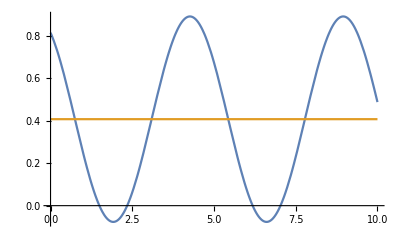

```mathematica
Plot[{(Cos[ω2 t]Cos[ϕ1]-Sin[ω2 t]Sin[ϕ1]) Cos[ζ1]( Cos[t ω2]), 1/2Cos[ϕ1] Cos[ζ1]},{t,0,10}]
```

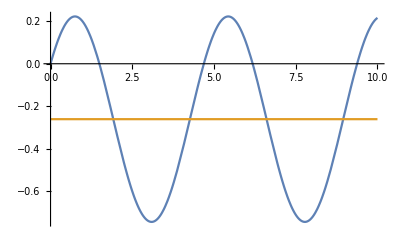

```mathematica
Plot[{(Cos[ω2 t]Cos[ϕ1]-Sin[ω2 t]Sin[ϕ1]) Cos[ζ1]( Sin[t ω2]),- 1/2Sin[ϕ1] Cos[ζ1]},{t,0,10}]
```

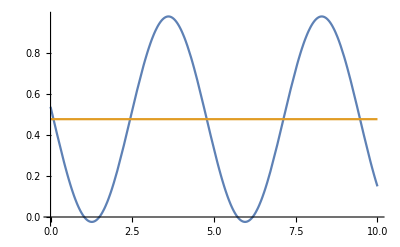

```mathematica
Plot[{(Cos[ω2 t]Cos[ϕ3]-Sin[ω2 t]Sin[ϕ3]) (Cos[ω2 t]Cos[ϕ1]-Sin[ω2 t]Sin[ϕ1]),1/2 Cos[ϕ3]Cos[ϕ1]+1/2 Sin[ϕ3]Sin[ϕ1]},{t,0,10}]
```

```mathematica
ωa = 1/2 ω12 Cos[ζ1];
ωb = 1/2 ω23 Cos[ζ3];
ωc=1/2 ω31 Cos[ζ3]  Cos[ζ1];
Heff=1/2 ωa(Cos[ϕ1]X1.X2+ Sin[ϕ1]X1.Y2)+1/2 ωb(Cos[ϕ3]X3.X2+ Sin[ϕ3]X3.Y2)+1/2 ωc(Cos[ϕ3]Cos[ϕ1]+Sin[ϕ3]Sin[ϕ1]) X3.X1  ;
```

### Now we can set ϕ1=ϕ3 = 0 and simplify further

```mathematica
Heff=1/2 ωa X1.X2+1/2 ωb X3.X2+1/2 ωc X3.X1  ;
```

### Alternatively we can set ϕ1=0 and ϕ3=π/2

```mathematica
Heff=1/2 ωa X1.X2+1/2 ωb X3.Y2  ;
```

### Now we can rotate into a three qubit basis

```mathematica
Ue = 1/(√2)(I0[3]-ⅈ Z1.Z3);
Ued = 1/(√2)(I0[3]+ⅈ Z1.Z3);

Max[Abs[-1/2 ωa Y1.Z3.X2-1/2 ωb Z1.Y3.Y2 -Ued.Heff.Ue]]
```

5.55112×10^-17

```mathematica
H3 = -1/2 ωa Y1.X2.Z3-1/2 ωb Z1.Y2.Y3 ;
```

### Finally we can turn off ωb by taking Ω3→0

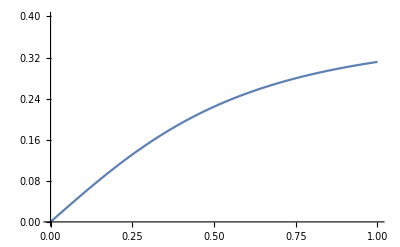

```mathematica
Plot[1/2 ω23 Cos[ArcTan[ω2/Ω3]],{Ω3,0,1},PlotRange->{0,0.4}]
```

```mathematica
H3eff = -1/2 ωa Y1.X2.Z3;
```

I have just turned a two qubit term into a three qubit term.  This seems like cheating.